# Boundary Equations

## equations of motion

```mathematica
ret[x_]:=ReplaceAll[x,retard]
subs1={t-> t0+Δθ/ω};
subs2={t0-> t-Δθ/ω};
 subs3={l1-> β1/ω,l2-> β2/ω};
retard={t-> t0};
η=DiagonalMatrix[{1,-1,-1,-1}];
x={t,l1 Cos[ω t],l1  Sin[ω t],0};
r={t,-l2 Cos[ω t],-l2 Sin[ω t],0};
u=D[x,t]; 
ur=D[r,t];
v=D[x,l1];vr=-D[r,l2];
```

```mathematica
dx=x-ret[r];
cons=dx.η.dx ω^2/.subs3/.subs2/.β1->β/.β2->β//Expand//Simplify
```

-2 β^2+Δθ^2-2 β^2 Cos[Δθ]

```mathematica
Δθrelativistic=FindRoot[ReplaceAll[cons,β->1]==0,{Δθ,1}]
```

{Δθ→1.47817}

```mathematica
1.4781702664303213/π
```

0.470516

```mathematica
cosθ=Solve[%==0,Cos[Δθ]][[1]]
```

{}⟦1⟧

```mathematica
γ1=1/(√(1-β1^2));
γ2=1/(√(1-β2^2));
```

```mathematica
F1=ReplaceAll[Table[q2/(ret[ur].η.(x-ret[r]))D[((x-ret[r])[[i]]ret[ur][[j]]-(x-ret[r])[[j]]ret[ur][[i]])/ret[ur].η.(x-ret[r]),t0],{i,4},{j,4}],subs2]//Simplify;
F2=ReplaceAll[Table[q1/(ret[u].η.(r-ret[x]))D[((r-ret[x])[[i]]ret[u][[j]]-(r-ret[x])[[j]]ret[u][[i]])/ret[u].η.(r-ret[x]),t0],{i,4},{j,4}],subs2]//Simplify;
```

```mathematica
eq1=Simplify[-T((u.η.v)u-(u.η.u)v)/(√((u.η.v)^2-(u.η.u)(v.η.v)))+m1 D[u/(√(u.η.u)),t]+Simplify[Replace[q1 u.η.F1,subs3,Infinity]]+(π ω^2)/2(a-S)/(β1+β2)^2(x-r)/Norm[x-r],β1>0&&β2>0&&ω>0]/.subs3/.t->0;
eq2=Simplify[T(((ur.η.vr)ur-(ur.η.ur)vr)/(√((ur.η.vr)^2-(ur.η.ur)(vr.η.vr))))+ m2 D[ur/(√(ur.η.ur)),t]+Simplify[ReplaceAll[q2 ur.η.F2,subs3]] +(π ω^2)/2(a-S)/(β1+β2)^2(r-x)/Norm[r-x],β1>0&&β2>0&&ω>0]/.subs3/.t->0;
```

```mathematica
AA1=(q2 ret[ur])/(ret[ur].η.(x-ret[r]))/.subs2/. subs3/.t->0//Simplify;
```

```mathematica
AA1
```

{(q2 ω)/(Δθ+β1 β2 Sin[Δθ]),-(q2 β2 ω Sin[Δθ])/(Δθ+β1 β2 Sin[Δθ]),-(q2 β2 ω Cos[Δθ])/(Δθ+β1 β2 Sin[Δθ]),0}

```mathematica
ReplaceAll[Refine[Distribute[eq1[[2]]],ω>0&&β1>0&&β2>0],{ω-> ω[β1],β2-> β2[β1],Δθ-> Δθ[β1],q1-> ze q1,m1->m ,m2-> m/z}]
ReplaceAll[Refine[Distribute[eq2[[2]]],ω>0&&β1>0&&β2>0],{ω-> ω[β1],β2-> β2[β1],Δθ-> Δθ[β1],q1-> ze q1,m1->m,m2-> m/z}]
```

T √(1-β1^2)-(m β1 ω[β1])/(√(1-β1^2))+(π (a-S) ω[β1]^2)/(2 (β1+β2[β1])^2)-1/(2 (β1 Sin[Δθ[β1]] β2[β1]+Δθ[β1])^3)q1 q2 ze (β1 (2+3 β2[β1]^2+2 β1^2 β2[β1]^2+2 β1 Cos[Δθ[β1]] β2[β1] (1+β2[β1]^2)+2 β1 Sin[Δθ[β1]] β2[β1] Δθ[β1])+β2[β1] (β1^2 Cos[Δθ[β1]]+β1 Cos[2 Δθ[β1]] β2[β1]+2 Sin[Δθ[β1]] Δθ[β1]+Cos[Δθ[β1]] (2+β1^2-2 Δθ[β1]^2))) ω[β1]^2

-T √(1-β2[β1]^2)+(m β2[β1] ω[β1])/(z √(1-β2[β1]^2))-(π (a-S) ω[β1]^2)/(2 (β1+β2[β1])^2)+1/(2 (β1 Sin[Δθ[β1]] β2[β1]+Δθ[β1])^3)q1 q2 ze (β2[β1] (2+3 β1^2+2 β1 (1+β1^2) Cos[Δθ[β1]] β2[β1]+2 β1^2 β2[β1]^2+2 β1 Sin[Δθ[β1]] β2[β1] Δθ[β1])+β1 (β1 Cos[2 Δθ[β1]] β2[β1]+Cos[Δθ[β1]] β2[β1]^2+2 Sin[Δθ[β1]] Δθ[β1]+Cos[Δθ[β1]] (2+β2[β1]^2-2 Δθ[β1]^2))) ω[β1]^2

```mathematica
Refine[Distribute[eq1[[2]]],ω>0&&β1>0&&β2>0]/.S-> Spin
```

T √(1-β1^2)-(m1 β1 ω)/(√(1-β1^2))+(π (a-Spin) ω^2)/(2 (β1+β2)^2)-1/(2 (Δθ+β1 β2 Sin[Δθ])^3)q1 q2 ω^2 (β2 (β1^2 Cos[Δθ]+(2+β1^2-2 Δθ^2) Cos[Δθ]+β1 β2 Cos[2 Δθ]+2 Δθ Sin[Δθ])+β1 (2+3 β2^2+2 β1^2 β2^2+2 β1 β2 (1+β2^2) Cos[Δθ]+2 β1 β2 Δθ Sin[Δθ]))

```mathematica
Simplify[Expand[ReplaceAll[eq1/(√(1-β1^2))+eq2/(√(1-β2^2)),{β2-> β1,m2->m1}]]]
```

{(q1 q2 β1^2 ω^2 (-2 Δθ Cos[Δθ]-2 (-1+Δθ^2) Sin[Δθ]+β1^2 (-2 Δθ+Sin[2 Δθ])))/(√(1-β1^2) (Δθ+β1^2 Sin[Δθ])^3),0,0,0}

```mathematica
Refine[Distribute[ReplaceAll[eq1[[2]],{β2-> β,β1->β,m2->m,m1->m,q1->q,q2->sign q}]],ω>0&&β>0]
Refine[Distribute[ReplaceAll[eq2[[2]],{β2-> β,β1->β,m2->m,m1->m,q1->q,q2->sign q}]],ω>0&&β>0]
```

T √(1-β^2)-(m β ω)/(√(1-β^2))+(π (a-S) ω^2)/(8 β^2)-(q^2 sign ω^2 (β (β^2 Cos[Δθ]+(2+β^2-2 Δθ^2) Cos[Δθ]+β^2 Cos[2 Δθ]+2 Δθ Sin[Δθ])+β (2+3 β^2+2 β^4+2 β^2 (1+β^2) Cos[Δθ]+2 β^2 Δθ Sin[Δθ])))/(2 (Δθ+β^2 Sin[Δθ])^3)

-T √(1-β^2)+(m β ω)/(√(1-β^2))-(π (a-S) ω^2)/(8 β^2)+(q^2 sign ω^2 (β (β^2 Cos[Δθ]+(2+β^2-2 Δθ^2) Cos[Δθ]+β^2 Cos[2 Δθ]+2 Δθ Sin[Δθ])+β (2+3 β^2+2 β^4+2 β^2 (1+β^2) Cos[Δθ]+2 β^2 Δθ Sin[Δθ])))/(2 (Δθ+β^2 Sin[Δθ])^3)

```mathematica
ω=ω/.Solve[T √(1-β^2)-(m β ω)/(√(1-β^2))+(π (a-S) ω^2)/(8 β^2)-1/(2 (Δθ+β^2 Sin[Δθ])^3)q^2 sign ω^2 (β (β^2 Cos[Δθ]+(2+β^2-2 Δθ^2) Cos[Δθ]+β^2 Cos[2 Δθ]+2 Δθ Sin[Δθ])+β (2+3 β^2+2 β^4+2 β^2 (1+β^2) Cos[Δθ]+2 β^2 Δθ Sin[Δθ]))==0,ω][[2]]/.S->Spin//Simplify
```

(4 (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+√2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (8 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ])))))/(√(1-β^2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ]))

## electric and magnetic fields

```mathematica
EField=F1[[2;;4,1]]/.subs3/.t->0//Simplify
```

{-((8 q2 (2 β1+β1 β2^2+2 β2 (1+β1^2-Δθ^2) Cos[Δθ]+β1 β2^2 Cos[2 Δθ]+2 β2 Δθ Sin[Δθ]) (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+√2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (8 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ]))))^2)/((-1+β^2) (Δθ+β1 β2 Sin[Δθ])^3 (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ])^2)),-((16 q2 β2 (β1 β2 Δθ+Δθ Cos[Δθ]+(-1+Δθ^2-β1 β2 Cos[Δθ]) Sin[Δθ]) (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+√2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (8 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ]))))^2)/((-1+β^2) (Δθ+β1 β2 Sin[Δθ])^3 (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ])^2)),0}

```mathematica
EField/.{β1->β,β2->β}//Simplify//MatrixForm
```

(-(8 q2 β (2+β^2+2 (1+β^2-Δθ^2) Cos[Δθ]+β^2 Cos[2 Δθ]+2 Δθ Sin[Δθ]) (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+√2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (8 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ]))))^2)/((-1+β^2) (Δθ+β^2 Sin[Δθ])^3 (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ])^2)
-(16 q2 β (β^2 Δθ+Δθ Cos[Δθ]+(-1+Δθ^2-β^2 Cos[Δθ]) Sin[Δθ]) (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+√2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (8 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ]))))^2)/((-1+β^2) (Δθ+β^2 Sin[Δθ])^3 (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ])^2)
0)

```mathematica
EField/.{β1->1,β2->1,Δθ-> 1.4}//Simplify//MatrixForm
```

(-(0.00406224 q2 (7.7612 m β^3+16.3892 m β^5+11.5362 m β^7+2.70675 m β^9-1. √(β^2 (1.4+0.98545 β^2)^3 (8 m^2 β^4 (1.4+0.98545 β^2)^3-37.4389 T √(1-β^2) (-1.+β^2) (q^2 sign β^3 (1.89446+2.34917 β^2+1. β^4)+a (-0.921023-1.9449 β^2-1.369 β^4-0.32121 β^6)+Spin (0.921023+1.9449 β^2+1.369 β^4+0.32121 β^6)))))^2)/((-1.+β^2) (q^2 sign β^3 (1.89446+2.34917 β^2+1. β^4)+a (-0.921023-1.9449 β^2-1.369 β^4-0.32121 β^6)+Spin (0.921023+1.9449 β^2+1.369 β^4+0.32121 β^6))^2)
-(0.00406422 q2 (7.7612 m β^3+16.3892 m β^5+11.5362 m β^7+2.70675 m β^9-1. √(β^2 (1.4+0.98545 β^2)^3 (8 m^2 β^4 (1.4+0.98545 β^2)^3-37.4389 T √(1-β^2) (-1.+β^2) (q^2 sign β^3 (1.89446+2.34917 β^2+1. β^4)+a (-0.921023-1.9449 β^2-1.369 β^4-0.32121 β^6)+Spin (0.921023+1.9449 β^2+1.369 β^4+0.32121 β^6)))))^2)/((-1.+β^2) (q^2 sign β^3 (1.89446+2.34917 β^2+1. β^4)+a (-0.921023-1.9449 β^2-1.369 β^4-0.32121 β^6)+Spin (0.921023+1.9449 β^2+1.369 β^4+0.32121 β^6))^2)
0)

```mathematica
BField/.{β1->1,β2->1,Δθ-> 1.4}//Simplify//MatrixForm
```

BField

```mathematica
Series[ReplaceAll[ReplaceAll[EField,ω-> β/l],{β1->β,β2->β}],{β,1,0}]//Normal//TrigExpand//Simplify//MatrixForm
```

(-(4 m q2 (6 m Δθ+4 m Δθ^3-6 m Δθ Cos[2 Δθ]+3 m Sin[Δθ]+12 m Δθ^2 Sin[Δθ]-4 √(m^2 (Δθ+Sin[Δθ])^6)-m Sin[3 Δθ]) (-6 a π+6 π Spin-22 a π β+22 π Spin β+13888 q^2 sign Δθ-7616 q^2 sign β Δθ+792 a π Δθ^2-792 π Spin Δθ^2-1128 a π β Δθ^2+1128 π Spin β Δθ^2-3072 q^2 sign Δθ^3+2048 q^2 sign β Δθ^3+1104 a π Δθ^4-1104 π Spin Δθ^4-1328 a π β Δθ^4+1328 π Spin β Δθ^4+128 q^2 sign Δθ^5+128 q^2 sign β Δθ^5+4 (16 q^2 sign Δθ (366-105 Δθ^2+β (-234+55 Δθ^2))+π Spin (-2-169 Δθ^2-148 Δθ^4+88 Δθ^6+β (6+215 Δθ^2+156 Δθ^4-104 Δθ^6))+a π (2+169 Δθ^2+148 Δθ^4-88 Δθ^6+β (-6-215 Δθ^2-156 Δθ^4+104 Δθ^6))) Cos[Δθ]+(128 q^2 sign Δθ (108-44 Δθ^2+Δθ^4+β (-92+28 Δθ^2+Δθ^4))+a π (13-608 Δθ^2-272 Δθ^4+β (21+928 Δθ^2+368 Δθ^4))-π Spin (13-608 Δθ^2-272 Δθ^4+β (21+928 Δθ^2+368 Δθ^4))) Cos[2 Δθ]-12 a π Cos[3 Δθ]+12 π Spin Cos[3 Δθ]+36 a π β Cos[3 Δθ]-36 π Spin β Cos[3 Δθ]+5248 q^2 sign Δθ Cos[3 Δθ]-5504 q^2 sign β Δθ Cos[3 Δθ]-678 a π Δθ^2 Cos[3 Δθ]+678 π Spin Δθ^2 Cos[3 Δθ]+858 a π β Δθ^2 Cos[3 Δθ]-858 π Spin β Δθ^2 Cos[3 Δθ]-1984 q^2 sign Δθ^3 Cos[3 Δθ]+2112 q^2 sign β Δθ^3 Cos[3 Δθ]+240 a π Δθ^4 Cos[3 Δθ]-240 π Spin Δθ^4 Cos[3 Δθ]-336 a π β Δθ^4 Cos[3 Δθ]+336 π Spin β Δθ^4 Cos[3 Δθ]-10 a π Cos[4 Δθ]+10 π Spin Cos[4 Δθ]+6 a π β Cos[4 Δθ]-6 π Spin β Cos[4 Δθ]+960 q^2 sign Δθ Cos[4 Δθ]-1088 q^2 sign β Δθ Cos[4 Δθ]-184 a π Δθ^2 Cos[4 Δθ]+184 π Spin Δθ^2 Cos[4 Δθ]+200 a π β Δθ^2 Cos[4 Δθ]-200 π Spin β Δθ^2 Cos[4 Δθ]+4 a π Cos[5 Δθ]-4 π Spin Cos[5 Δθ]-12 a π β Cos[5 Δθ]+12 π Spin β Cos[5 Δθ]+2 a π Δθ^2 Cos[5 Δθ]-2 π Spin Δθ^2 Cos[5 Δθ]+2 a π β Δθ^2 Cos[5 Δθ]-2 π Spin β Δθ^2 Cos[5 Δθ]+3 a π Cos[6 Δθ]-3 π Spin Cos[6 Δθ]-5 a π β Cos[6 Δθ]+5 π Spin β Cos[6 Δθ]-6624 q^2 sign Sin[Δθ]+9760 q^2 sign β Sin[Δθ]+268 a π Δθ Sin[Δθ]-268 π Spin Δθ Sin[Δθ]-532 a π β Δθ Sin[Δθ]+532 π Spin β Δθ Sin[Δθ]+9920 q^2 sign Δθ^2 Sin[Δθ]-6976 q^2 sign β Δθ^2 Sin[Δθ]+2128 a π Δθ^3 Sin[Δθ]-2128 π Spin Δθ^3 Sin[Δθ]-2736 a π β Δθ^3 Sin[Δθ]+2736 π Spin β Δθ^3 Sin[Δθ]-704 q^2 sign Δθ^4 Sin[Δθ]+832 q^2 sign β Δθ^4 Sin[Δθ]+352 a π Δθ^5 Sin[Δθ]-352 π Spin Δθ^5 Sin[Δθ]-416 a π β Δθ^5 Sin[Δθ]+416 π Spin β Δθ^5 Sin[Δθ]-7808 q^2 sign Sin[2 Δθ]+11136 q^2 sign β Sin[2 Δθ]+256 a π Δθ Sin[2 Δθ]-256 π Spin Δθ Sin[2 Δθ]-384 a π β Δθ Sin[2 Δθ]+384 π Spin β Δθ Sin[2 Δθ]+9856 q^2 sign Δθ^2 Sin[2 Δθ]-9088 q^2 sign β Δθ^2 Sin[2 Δθ]+1216 a π Δθ^3 Sin[2 Δθ]-1216 π Spin Δθ^3 Sin[2 Δθ]-1408 a π β Δθ^3 Sin[2 Δθ]+1408 π Spin β Δθ^3 Sin[2 Δθ]-1408 q^2 sign Δθ^4 Sin[2 Δθ]+640 q^2 sign β Δθ^4 Sin[2 Δθ]-512 a π Δθ^5 Sin[2 Δθ]+512 π Spin Δθ^5 Sin[2 Δθ]+640 a π β Δθ^5 Sin[2 Δθ]-640 π Spin β Δθ^5 Sin[2 Δθ]-4432 q^2 sign Sin[3 Δθ]+6064 q^2 sign β Sin[3 Δθ]-6 a π Δθ Sin[3 Δθ]+6 π Spin Δθ Sin[3 Δθ]+74 a π β Δθ Sin[3 Δθ]-74 π Spin β Δθ Sin[3 Δθ]+4032 q^2 sign Δθ^2 Sin[3 Δθ]-4672 q^2 sign β Δθ^2 Sin[3 Δθ]+144 a π Δθ^3 Sin[3 Δθ]-144 π Spin Δθ^3 Sin[3 Δθ]-112 a π β Δθ^3 Sin[3 Δθ]+112 π Spin β Δθ^3 Sin[3 Δθ]-704 q^2 sign Δθ^4 Sin[3 Δθ]+832 q^2 sign β Δθ^4 Sin[3 Δθ]-1216 q^2 sign Sin[4 Δθ]+1600 q^2 sign β Sin[4 Δθ]-128 a π Δθ Sin[4 Δθ]+128 π Spin Δθ Sin[4 Δθ]+192 a π β Δθ Sin[4 Δθ]-192 π Spin β Δθ Sin[4 Δθ]+576 q^2 sign Δθ^2 Sin[4 Δθ]-704 q^2 sign β Δθ^2 Sin[4 Δθ]+32 a π Δθ^3 Sin[4 Δθ]-32 π Spin Δθ^3 Sin[4 Δθ]-64 a π β Δθ^3 Sin[4 Δθ]+64 π Spin β Δθ^3 Sin[4 Δθ]-112 q^2 sign Sin[5 Δθ]+144 q^2 sign β Sin[5 Δθ]-50 a π Δθ Sin[5 Δθ]+50 π Spin Δθ Sin[5 Δθ]+62 a π β Δθ Sin[5 Δθ]-62 π Spin β Δθ Sin[5 Δθ]))/((-1+β) (Δθ+Sin[Δθ]) (112 q^2 sign-6 a π Δθ+6 π Spin Δθ-4 a π Δθ^3+4 π Spin Δθ^3-32 q^2 sign (-4+Δθ^2) Cos[Δθ]+2 (8 q^2 sign+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π Sin[Δθ]+3 π Spin Sin[Δθ]+64 q^2 sign Δθ Sin[Δθ]-12 a π Δθ^2 Sin[Δθ]+12 π Spin Δθ^2 Sin[Δθ]+a π Sin[3 Δθ]-π Spin Sin[3 Δθ])^3)
(4 m q2 (6 m Δθ+4 m Δθ^3-6 m Δθ Cos[2 Δθ]+3 m Sin[Δθ]+12 m Δθ^2 Sin[Δθ]-4 √(m^2 (Δθ+Sin[Δθ])^6)-m Sin[3 Δθ]) (-2144 q^2 sign+3232 q^2 sign β+60 a π Δθ-60 π Spin Δθ-132 a π β Δθ+132 π Spin β Δθ-3264 q^2 sign Δθ^2-448 q^2 sign β Δθ^2-448 a π Δθ^3+448 π Spin Δθ^3+608 a π β Δθ^3-608 π Spin β Δθ^3-1152 q^2 sign Δθ^4+896 q^2 sign β Δθ^4-992 a π Δθ^5+992 π Spin Δθ^5+1184 a π β Δθ^5-1184 π Spin β Δθ^5+4 (8 q^2 sign (-73-352 Δθ^2-46 Δθ^4+β (103+208 Δθ^2+66 Δθ^4))+π (a-Spin) Δθ (25+36 Δθ^2-88 Δθ^4+β (-31-28 Δθ^2+104 Δθ^4))) Cos[Δθ]-16 (8 q^2 sign (-9+82 Δθ^2-11 Δθ^4+β (15-78 Δθ^2+5 Δθ^4))+π (a-Spin) Δθ (5-30 Δθ^2-32 Δθ^4+β (-11+42 Δθ^2+40 Δθ^4))) Cos[2 Δθ]+2224 q^2 sign Cos[3 Δθ]-3152 q^2 sign β Cos[3 Δθ]-150 a π Δθ Cos[3 Δθ]+150 π Spin Δθ Cos[3 Δθ]+186 a π β Δθ Cos[3 Δθ]-186 π Spin β Δθ Cos[3 Δθ]-3072 q^2 sign Δθ^2 Cos[3 Δθ]+3584 q^2 sign β Δθ^2 Cos[3 Δθ]-144 a π Δθ^3 Cos[3 Δθ]+144 π Spin Δθ^3 Cos[3 Δθ]+112 a π β Δθ^3 Cos[3 Δθ]-112 π Spin β Δθ^3 Cos[3 Δθ]+704 q^2 sign Δθ^4 Cos[3 Δθ]-832 q^2 sign β Δθ^4 Cos[3 Δθ]+992 q^2 sign Cos[4 Δθ]-1312 q^2 sign β Cos[4 Δθ]+20 a π Δθ Cos[4 Δθ]-20 π Spin Δθ Cos[4 Δθ]-44 a π β Δθ Cos[4 Δθ]+44 π Spin β Δθ Cos[4 Δθ]-576 q^2 sign Δθ^2 Cos[4 Δθ]+704 q^2 sign β Δθ^2 Cos[4 Δθ]-32 a π Δθ^3 Cos[4 Δθ]+32 π Spin Δθ^3 Cos[4 Δθ]+64 a π β Δθ^3 Cos[4 Δθ]-64 π Spin β Δθ^3 Cos[4 Δθ]+112 q^2 sign Cos[5 Δθ]-144 q^2 sign β Cos[5 Δθ]+50 a π Δθ Cos[5 Δθ]-50 π Spin Δθ Cos[5 Δθ]-62 a π β Δθ Cos[5 Δθ]+62 π Spin β Δθ Cos[5 Δθ]-20 a π Sin[Δθ]+20 π Spin Sin[Δθ]-20 a π β Sin[Δθ]+20 π Spin β Sin[Δθ]+12672 q^2 sign Δθ Sin[Δθ]-11904 q^2 sign β Δθ Sin[Δθ]+164 a π Δθ^2 Sin[Δθ]-164 π Spin Δθ^2 Sin[Δθ]-220 a π β Δθ^2 Sin[Δθ]+220 π Spin β Δθ^2 Sin[Δθ]-5824 q^2 sign Δθ^3 Sin[Δθ]+2368 q^2 sign β Δθ^3 Sin[Δθ]-1904 a π Δθ^4 Sin[Δθ]+1904 π Spin Δθ^4 Sin[Δθ]+2384 a π β Δθ^4 Sin[Δθ]-2384 π Spin β Δθ^4 Sin[Δθ]-352 a π Δθ^6 Sin[Δθ]+352 π Spin Δθ^6 Sin[Δθ]+416 a π β Δθ^6 Sin[Δθ]-416 π Spin β Δθ^6 Sin[Δθ]+15 a π Sin[2 Δθ]-15 π Spin Sin[2 Δθ]-25 a π β Sin[2 Δθ]+25 π Spin β Sin[2 Δθ]+10368 q^2 sign Δθ Sin[2 Δθ]-10112 q^2 sign β Δθ Sin[2 Δθ]+368 a π Δθ^2 Sin[2 Δθ]-368 π Spin Δθ^2 Sin[2 Δθ]-400 a π β Δθ^2 Sin[2 Δθ]+400 π Spin β Δθ^2 Sin[2 Δθ]-7936 q^2 sign Δθ^3 Sin[2 Δθ]+6400 q^2 sign β Δθ^3 Sin[2 Δθ]-272 a π Δθ^4 Sin[2 Δθ]+272 π Spin Δθ^4 Sin[2 Δθ]+368 a π β Δθ^4 Sin[2 Δθ]-368 π Spin β Δθ^4 Sin[2 Δθ]+128 q^2 sign Δθ^5 Sin[2 Δθ]+128 q^2 sign β Δθ^5 Sin[2 Δθ]+10 a π Sin[3 Δθ]-10 π Spin Sin[3 Δθ]+10 a π β Sin[3 Δθ]-10 π Spin β Sin[3 Δθ]+3968 q^2 sign Δθ Sin[3 Δθ]-4224 q^2 sign β Δθ Sin[3 Δθ]-58 a π Δθ^2 Sin[3 Δθ]+58 π Spin Δθ^2 Sin[3 Δθ]+70 a π β Δθ^2 Sin[3 Δθ]-70 π Spin β Δθ^2 Sin[3 Δθ]-1984 q^2 sign Δθ^3 Sin[3 Δθ]+2112 q^2 sign β Δθ^3 Sin[3 Δθ]+240 a π Δθ^4 Sin[3 Δθ]-240 π Spin Δθ^4 Sin[3 Δθ]-336 a π β Δθ^4 Sin[3 Δθ]+336 π Spin β Δθ^4 Sin[3 Δθ]-12 a π Sin[4 Δθ]+12 π Spin Sin[4 Δθ]+20 a π β Sin[4 Δθ]-20 π Spin β Sin[4 Δθ]+960 q^2 sign Δθ Sin[4 Δθ]-1088 q^2 sign β Δθ Sin[4 Δθ]-184 a π Δθ^2 Sin[4 Δθ]+184 π Spin Δθ^2 Sin[4 Δθ]+200 a π β Δθ^2 Sin[4 Δθ]-200 π Spin β Δθ^2 Sin[4 Δθ]-2 a π Sin[5 Δθ]+2 π Spin Sin[5 Δθ]-2 a π β Sin[5 Δθ]+2 π Spin β Sin[5 Δθ]+2 a π Δθ^2 Sin[5 Δθ]-2 π Spin Δθ^2 Sin[5 Δθ]+2 a π β Δθ^2 Sin[5 Δθ]-2 π Spin β Δθ^2 Sin[5 Δθ]+3 a π Sin[6 Δθ]-3 π Spin Sin[6 Δθ]-5 a π β Sin[6 Δθ]+5 π Spin β Sin[6 Δθ]))/((-1+β) (Δθ+Sin[Δθ]) (112 q^2 sign-6 a π Δθ+6 π Spin Δθ-4 a π Δθ^3+4 π Spin Δθ^3-32 q^2 sign (-4+Δθ^2) Cos[Δθ]+2 (8 q^2 sign+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π Sin[Δθ]+3 π Spin Sin[Δθ]+64 q^2 sign Δθ Sin[Δθ]-12 a π Δθ^2 Sin[Δθ]+12 π Spin Δθ^2 Sin[Δθ]+a π Sin[3 Δθ]-π Spin Sin[3 Δθ])^3)
0)

```mathematica
%/.Δθrelativistic//MatrixForm
```

(-(1.61689 m (60.5617 m-60.5617 √(m^2)) q2 (50513.3 a-6 a π+24299.6 q^2 sign-50494.4 Spin-65325. a β-22 a π β-7153.83 q^2 sign β+65394.1 Spin β+0.369975 (a π (159.868-135.667 β)+23.6507 q^2 sign (136.576-113.826 β)+π Spin (-159.868+135.667 β))-0.98289 (189.206 q^2 sign (16.6347-26.0462 β)+a π (-2614.05+3805.56 β)-π Spin (-2614.05+3805.56 β))))/((-162.874 a+211.569 q^2 sign-1.96578 (8 q^2 sign+13.9314 (a-Spin))+162.874 Spin)^3 (-1+β))
(1.61689 m (60.5617 m-60.5617 √(m^2)) q2 (-67546.8 a-16467.4 q^2 sign+67546.8 Spin+83483.7 a β-2174.39 q^2 sign β-83483.7 Spin β+15.7262 (8 q^2 sign (117.653-131.558 β)+4.64381 (a-Spin) (-213.323+271.736 β))+0.369975 (4.64381 (a-Spin) (-316.467+404.334 β)+8 q^2 sign (-1061.73+872.573 β))))/((-162.874 a+211.569 q^2 sign-1.96578 (8 q^2 sign+13.9314 (a-Spin))+162.874 Spin)^3 (-1+β))
0)

```mathematica
Refine[Norm[%],q2>0&&l>0]
```

√(2.61434 q2^2 Abs[(m (60.5617 m-60.5617 √(m^2)) (-67546.8 a-16467.4 q^2 sign+67546.8 Spin+83483.7 a β-2174.39 q^2 sign β-83483.7 Spin β+15.7262 (8 q^2 sign (117.653-131.558 β)+4.64381 (a-Spin) (-213.323+271.736 β))+0.369975 (4.64381 (a-Spin) (-316.467+404.334 β)+8 q^2 sign (-1061.73+872.573 β))))/((-162.874 a+211.569 q^2 sign-1.96578 (8 q^2 sign+13.9314 (a-Spin))+162.874 Spin)^3 (-1+β))]^2+2.61434 q2^2 Abs[(m (60.5617 m-60.5617 √(m^2)) (50513.3 a-6 a π+24299.6 q^2 sign-50494.4 Spin-65325. a β-22 a π β-7153.83 q^2 sign β+65394.1 Spin β+0.369975 (a π (159.868-135.667 β)+23.6507 q^2 sign (136.576-113.826 β)+π Spin (-159.868+135.667 β))-0.98289 (189.206 q^2 sign (16.6347-26.0462 β)+a π (-2614.05+3805.56 β)-π Spin (-2614.05+3805.56 β))))/((-162.874 a+211.569 q^2 sign-1.96578 (8 q^2 sign+13.9314 (a-Spin))+162.874 Spin)^3 (-1+β))]^2)

```mathematica
LeviCivitaTensor[2]//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
BField=-1/2 Table[Sum[Drop[F1[[i,j]]]LeviCivitaTensor[3][[i-1,j-1,k-1]],{i,2,4},{j,2,4}],{k,2,4}]/.subs3/.t->0//Simplify
```

{0,0,-((16 q2 β2 (β2+β1^2 β2+β1 (1+β2^2) Cos[Δθ]+β1 Δθ Sin[Δθ]) (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+√2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (8 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ]))))^2)/((-1+β^2) (Δθ+β1 β2 Sin[Δθ])^3 (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ])^2))}

```mathematica
BField/.{β1->β,β2->β}//Simplify//MatrixForm
```

(0
0
-(16 q2 β^2 (1+β^2+(1+β^2) Cos[Δθ]+Δθ Sin[Δθ]) (-6 m β^7 Δθ-4 m β^3 Δθ^3+6 m β^7 Δθ Cos[2 Δθ]-3 m β^9 Sin[Δθ]-12 m β^5 Δθ^2 Sin[Δθ]+m β^9 Sin[3 Δθ]+√2 √(β^2 (Δθ+β^2 Sin[Δθ])^3 (8 m^2 β^4 (Δθ+β^2 Sin[Δθ])^3+T (1-β^2)^(3/2) (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ]))))^2)/((-1+β^2) (Δθ+β^2 Sin[Δθ])^3 (32 q^2 sign β^3+48 q^2 sign β^5+32 q^2 sign β^7-6 a π β^4 Δθ+6 π Spin β^4 Δθ-4 a π Δθ^3+4 π Spin Δθ^3+32 q^2 sign β^3 (1+2 β^2+β^4-Δθ^2) Cos[Δθ]+2 β^4 (8 q^2 sign β+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π β^6 Sin[Δθ]+3 π Spin β^6 Sin[Δθ]+32 q^2 sign β^3 Δθ Sin[Δθ]+32 q^2 sign β^5 Δθ Sin[Δθ]-12 a π β^2 Δθ^2 Sin[Δθ]+12 π Spin β^2 Δθ^2 Sin[Δθ]+a π β^6 Sin[3 Δθ]-π Spin β^6 Sin[3 Δθ])^2))

```mathematica
Series[ReplaceAll[ReplaceAll[BField,ω-> β/l],{β1->β,β2->β}],{β,1,0}]//Normal//Simplify//MatrixForm
```

(0
0
(4 q2 (-(2 (Δθ+Sin[Δθ]) (2+2 Cos[Δθ]+Δθ Sin[Δθ]) (6 m Δθ+4 m Δθ^3-6 m Δθ Cos[2 Δθ]+3 m Sin[Δθ]+12 m Δθ^2 Sin[Δθ]-4 √(m^2 (Δθ+Sin[Δθ])^6)-m Sin[3 Δθ])^2 (112 q^2 sign-6 a π Δθ+6 π Spin Δθ-4 a π Δθ^3+4 π Spin Δθ^3-32 q^2 sign (-4+Δθ^2) Cos[Δθ]+2 (8 q^2 sign+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π Sin[Δθ]+3 π Spin Sin[Δθ]+64 q^2 sign Δθ Sin[Δθ]-12 a π Δθ^2 Sin[Δθ]+12 π Spin Δθ^2 Sin[Δθ]+a π Sin[3 Δθ]-π Spin Sin[3 Δθ]))/(-1+β)-(-6 m Δθ-4 m Δθ^3+6 m Δθ Cos[2 Δθ]-3 m Sin[Δθ]-12 m Δθ^2 Sin[Δθ]+4 √(m^2 (Δθ+Sin[Δθ])^6)+m Sin[3 Δθ]) (-24 Cos[Δθ/2] (2 Cos[Δθ/2]+Δθ Sin[Δθ/2]) (Δθ+3 Sin[Δθ]) (6 m Δθ+4 m Δθ^3-6 m Δθ Cos[2 Δθ]+3 m Sin[Δθ]+12 m Δθ^2 Sin[Δθ]-4 √(m^2 (Δθ+Sin[Δθ])^6)-m Sin[3 Δθ]) (112 q^2 sign-6 a π Δθ+6 π Spin Δθ-4 a π Δθ^3+4 π Spin Δθ^3-32 q^2 sign (-4+Δθ^2) Cos[Δθ]+2 (8 q^2 sign+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π Sin[Δθ]+3 π Spin Sin[Δθ]+64 q^2 sign Δθ Sin[Δθ]-12 a π Δθ^2 Sin[Δθ]+12 π Spin Δθ^2 Sin[Δθ]+a π Sin[3 Δθ]-π Spin Sin[3 Δθ])+(-6 m Δθ-4 m Δθ^3+6 m Δθ Cos[2 Δθ]-3 m Sin[Δθ]-12 m Δθ^2 Sin[Δθ]+4 √(m^2 (Δθ+Sin[Δθ])^6)+m Sin[3 Δθ]) (-(10 Δθ+10 Δθ Cos[Δθ]+(-14+3 Δθ^2) Sin[Δθ]-9 Δθ Sin[Δθ]^2-7 Sin[2 Δθ]) (-112 q^2 sign+6 a π Δθ-6 π Spin Δθ+4 a π Δθ^3-4 π Spin Δθ^3+32 q^2 sign (-4+Δθ^2) Cos[Δθ]-2 (8 q^2 sign+3 π (a-Spin) Δθ) Cos[2 Δθ]+3 a π Sin[Δθ]-3 π Spin Sin[Δθ]-64 q^2 sign Δθ Sin[Δθ]+12 a π Δθ^2 Sin[Δθ]-12 π Spin Δθ^2 Sin[Δθ]-a π Sin[3 Δθ]+π Spin Sin[3 Δθ])+8 (Δθ+Sin[Δθ]) (2+2 Cos[Δθ]+Δθ Sin[Δθ]) (-280 q^2 sign+12 a π Δθ-12 π Spin Δθ+16 q^2 sign (-20+3 Δθ^2) Cos[Δθ]-4 (10 q^2 sign+3 π (a-Spin) Δθ) Cos[2 Δθ]+9 a π Sin[Δθ]-9 π Spin Sin[Δθ]-128 q^2 sign Δθ Sin[Δθ]+12 a π Δθ^2 Sin[Δθ]-12 π Spin Δθ^2 Sin[Δθ]-3 a π Sin[3 Δθ]+3 π Spin Sin[3 Δθ])))))/((Δθ+Sin[Δθ])^4 (112 q^2 sign-6 a π Δθ+6 π Spin Δθ-4 a π Δθ^3+4 π Spin Δθ^3-32 q^2 sign (-4+Δθ^2) Cos[Δθ]+2 (8 q^2 sign+3 π (a-Spin) Δθ) Cos[2 Δθ]-3 a π Sin[Δθ]+3 π Spin Sin[Δθ]+64 q^2 sign Δθ Sin[Δθ]-12 a π Δθ^2 Sin[Δθ]+12 π Spin Δθ^2 Sin[Δθ]+a π Sin[3 Δθ]-π Spin Sin[3 Δθ])^3))

```mathematica
%/.Δθrelativistic//MatrixForm
```

(0
0
(0.106793 q2 (-(-60.5617 m+60.5617 √(m^2)) ((-60.5617 m+60.5617 √(m^2)) (72.3724 (174.961 a-488.292 q^2 sign+3.93156 (10 q^2 sign+13.9314 (a-Spin))-174.961 Spin)+5.74329 (162.874 a-211.569 q^2 sign+1.96578 (8 q^2 sign+13.9314 (a-Spin))-162.874 Spin))-195.946 (60.5617 m-60.5617 √(m^2)) (-162.874 a+211.569 q^2 sign-1.96578 (8 q^2 sign+13.9314 (a-Spin))+162.874 Spin))-(18.0931 (60.5617 m-60.5617 √(m^2))^2 (-162.874 a+211.569 q^2 sign-1.96578 (8 q^2 sign+13.9314 (a-Spin))+162.874 Spin))/(-1+β)))/((-162.874 a+211.569 q^2 sign-1.96578 (8 q^2 sign+13.9314 (a-Spin))+162.874 Spin)^3))

```mathematica
Series[ReplaceAll[BField,{β1->β,β2->β,Δθ->2β,ω-> (2β)/L}],{β,0,1}]//Normal
```

{0,0,-(2 q2 T β)/(a π-2 q^2 sign-π Spin)}

```mathematica
Series[ReplaceAll[EField,{β1->β,β2->β,Δθ->2β,ω-> (2β)/L}],{β,0,1}]//Normal
```

{-(2 q2 T)/(a π-2 q^2 sign-π Spin),0,0}

```mathematica
Series[ReplaceAll[AA1,{β1->β,β2->β,Δθ->2β,ω-> (2β)/L}],{β,0,1}]//Normal
```

{(2 q2 β)/(L (Δθ+β1 β2 Sin[Δθ])),0,(√2 q2 √(-(a π-2 q^2 sign-π Spin) T) β)/(a π-2 q^2 sign-π Spin),0}

# outward radiation

## Classical calculation

### lower bound

poynting vector is given by
S^i=F^(0ν)F_ν^i

```mathematica
η=DiagonalMatrix[{1,-1,-1,-1}];
x={t0,l1 Cos[ω t0],l1  Sin[ω t0],0};
r={t0,-l2 Cos[ω t0],-l2 Sin[ω t0],0};
y={t,y1,y2,y3};
dx=y-x;dr=y-r;
```

```mathematica
retard={t-> t0};
ret[x_]:=ReplaceAll[x,retard]
subs1=Solve[dx.η.dx==0,t][[2]];
subs2=Solve[dr.η.dr==0,t][[2]];
subs3={l1-> β1/ω,l2-> β2/ω};
```

```mathematica
u=D[x,t0]; 
ur=D[r,t0];
```

```mathematica
F1=ReplaceAll[Table[q2/(ur.η.dr)D[(dr[[i]]ur[[j]]-dr[[j]]ur[[i]])/(ur.η.dr),t0],{i,4},{j,4}],subs2]//Simplify;
F2=ReplaceAll[Table[q1/(u.η.dx)D[(dx[[i]]u[[j]]-dx[[j]]u[[i]])/(u.η.dx),t0],{i,4},{j,4}],subs1]//Simplify;
```

```mathematica
F=F1+F2;
SPoynting=(F.η.F)[[1,2;;4]];
SPoynting1=(F1.η.F1)[[1,2;;4]];
nVec={Sin[φ]Cos[θ],Sin[φ]Sin[θ],Cos[φ]};
```

```mathematica
toSpherical={y3-> R Cos[φ],y1-> R Sin[φ]Cos[θ],y2-> R Sin[φ]Sin[θ]};
sss=Normal[Series[ReplaceAll[SPoynting,toSpherical],{R,∞,2}]];
```

```mathematica
Pd=sss.nVec;
```

We now have to integrate the power over angles, and average over time.

```mathematica
Pd=Pd/.subs3//Expand;
```

when β->0

```mathematica
PP=2π ω Integrate[Integrate[Normal[Series[R^2 Pd Sin[φ],{β1,0,2},{β2,0,2}]],{t0,0,1/(2π ω)}],{θ,0,2π},{φ,0,π}]
```

8/15 π (5 q1^2 β1^2+5 q2^2 β2^2+2 q1 q2 β1 β2 (-5+8 β1 β2)) ω^2

for the case where there wasn’t any electric charge we had:

```mathematica
force=ω-> T/(γ^2 m β);
```

```mathematica
Simplify[ReplaceAll[ReplaceAll[ReplaceAll[PP,force],{β1->β,β2->β,q2-> -q1,T-> 1/(2π α),γ-> 1/(√(1-β^2))}],{q1-> 1/(√137),α-> 0.9 GeV^-2}]]
```

-(0.00611932 GeV^4 (-1.+β^2)^2 (-1.25+1. β^2))/m^2

```mathematica
τ[δE_,m_,β_]:=Block[{δt},
δt=δt/.Solve[-(0.006119321352846897 GeV^4 (-1+β^2)^2 (-1.25+β^2))/m^2==δE/δt,δt][[1]]/.{β-> 0.7, MeV-> 10^6 eV,GeV-> 10^9 eV}/.eV-> (6.58 10^-16 s)^-1;
δt]
SetAttributes[τ,Listable];
Γ[δE_,m_,β_]:=Block[{δt},
δt=δt/.Solve[-(0.006119321352846897 GeV^4 (-1+β^2)^2 (-1.25+β^2))/m^2==δE/δt,δt][[1]]/.{β-> 0.7,GeV-> 10^3 MeV};
δt^-1]
SetAttributes[Γ,Listable];
```

```mathematica
Γ[100 MeV,100MeV,0.7]
```

1209.64 MeV

### upper bound

poynting vector is given by
S^i=F^(0ν)F_ν^i

```mathematica
η=DiagonalMatrix[{1,-1,-1,-1}];
x={t0,l1 Cos[ω t0],l1  Sin[ω t0],0};
r={t0,-l2 Cos[ω t0],-l2 Sin[ω t0],0};
y={t,y1,y2,y3};
dx=y-x;dr=y-r;
```

```mathematica
retard={t-> t0};
ret[x_]:=ReplaceAll[x,retard]
subs1=Solve[dx.η.dx==0,t][[2]];
subs2=Solve[dr.η.dr==0,t][[2]];
subs3={l1-> β1/ω,l2-> β2/ω};
```

```mathematica
u=D[x,t0]; 
ur=D[r,t0];
```

```mathematica
F1=ReplaceAll[Table[q2/(ur.η.dr)D[(dr[[i]]ur[[j]]-dr[[j]]ur[[i]])/(ur.η.dr),t0],{i,4},{j,4}],subs2]//Simplify;
F2=ReplaceAll[Table[q1/(u.η.dx)D[(dx[[i]]u[[j]]-dx[[j]]u[[i]])/(u.η.dx),t0],{i,4},{j,4}],subs1]//Simplify;
```

```mathematica
F=F1+F2;
SPoynting=(F.η.F)[[1,2;;4]];
SPoynting1=(F1.η.F1)[[1,2;;4]];
nVec={Sin[φ]Cos[θ],Sin[φ]Sin[θ],Cos[φ]};
```

```mathematica
toSpherical={y3-> R Cos[φ],y1-> R Sin[φ]Cos[θ],y2-> R Sin[φ]Sin[θ]};
sss=Normal[Series[ReplaceAll[SPoynting,toSpherical],{R,∞,2}]];
```

```mathematica
Pd=sss.nVec;
```

We now have to integrate the power over angles, and average over time.

```mathematica
Pd=ReplaceAll[ReplaceAll[Pd,subs3],{β1->β,β2->β,q2->-q1}]//Simplify
```

-((q1^2 β^2 ω^2 (-6144+2304 β^2+288 β^4-960 β^6-700 β^8+16 (-128-192 β^2-39 β^4+90 β^6+70 β^8) Cos[2 φ]-16 β^2 (-48-30 β^2+36 β^4+35 β^6) Cos[4 φ]-144 β^4 Cos[6 φ]+96 β^6 Cos[6 φ]+160 β^8 Cos[6 φ]-20 β^8 Cos[8 φ]+β^8 Cos[6 θ-8 φ-6 t0 ω]+216 β^4 Cos[6 θ-4 φ-6 t0 ω]-144 β^6 Cos[6 θ-4 φ-6 t0 ω]+28 β^8 Cos[6 θ-4 φ-6 t0 ω]+216 β^4 Cos[6 θ+4 φ-6 t0 ω]-144 β^6 Cos[6 θ+4 φ-6 t0 ω]+28 β^8 Cos[6 θ+4 φ-6 t0 ω]+β^8 Cos[6 θ+8 φ-6 t0 ω]+72 β^4 Cos[4 θ-6 φ-4 t0 ω]-48 β^6 Cos[4 θ-6 φ-4 t0 ω]+48 β^8 Cos[4 θ-6 φ-4 t0 ω]+72 β^4 Cos[4 θ+6 φ-4 t0 ω]-48 β^6 Cos[4 θ+6 φ-4 t0 ω]+48 β^8 Cos[4 θ+6 φ-4 t0 ω]-540 β^4 Cos[2 (3 θ+φ-3 t0 ω)]+360 β^6 Cos[2 (3 θ+φ-3 t0 ω)]-56 β^8 Cos[2 (3 θ+φ-3 t0 ω)]+1536 β^2 Cos[2 (2 θ+φ-2 t0 ω)]-1736 β^4 Cos[2 (2 θ+φ-2 t0 ω)]-720 β^6 Cos[2 (2 θ+φ-2 t0 ω)]+336 β^8 Cos[2 (2 θ+φ-2 t0 ω)]+2048 Cos[2 (θ-t0 ω)]-3792 β^4 Cos[2 (θ-t0 ω)]+480 β^6 Cos[2 (θ-t0 ω)]+1050 β^8 Cos[2 (θ-t0 ω)]-2304 β^2 Cos[4 (θ-t0 ω)]+2784 β^4 Cos[4 (θ-t0 ω)]+960 β^6 Cos[4 (θ-t0 ω)]-420 β^8 Cos[4 (θ-t0 ω)]+720 β^4 Cos[6 (θ-t0 ω)]-480 β^6 Cos[6 (θ-t0 ω)]+70 β^8 Cos[6 (θ-t0 ω)]+15 β^8 Cos[2 (θ-4 φ-t0 ω)]+36 β^4 Cos[2 (θ-3 φ-t0 ω)]-24 β^6 Cos[2 (θ-3 φ-t0 ω)]-120 β^8 Cos[2 (θ-3 φ-t0 ω)]-728 β^4 Cos[2 (θ-2 φ-t0 ω)]+144 β^6 Cos[2 (θ-2 φ-t0 ω)]+420 β^8 Cos[2 (θ-2 φ-t0 ω)]-6 β^8 Cos[4 (θ-2 φ-t0 ω)]-1024 Cos[2 (θ+φ-t0 ω)]+2588 β^4 Cos[2 (θ+φ-t0 ω)]-360 β^6 Cos[2 (θ+φ-t0 ω)]-840 β^8 Cos[2 (θ+φ-t0 ω)]-384 β^2 Cos[4 (θ+φ-t0 ω)]+272 β^4 Cos[4 (θ+φ-t0 ω)]+288 β^6 Cos[4 (θ+φ-t0 ω)]-168 β^8 Cos[4 (θ+φ-t0 ω)]-36 β^4 Cos[6 (θ+φ-t0 ω)]+24 β^6 Cos[6 (θ+φ-t0 ω)]-8 β^8 Cos[6 (θ+φ-t0 ω)]-728 β^4 Cos[2 (θ+2 φ-t0 ω)]+144 β^6 Cos[2 (θ+2 φ-t0 ω)]+420 β^8 Cos[2 (θ+2 φ-t0 ω)]-6 β^8 Cos[4 (θ+2 φ-t0 ω)]+36 β^4 Cos[2 (θ+3 φ-t0 ω)]-24 β^6 Cos[2 (θ+3 φ-t0 ω)]-120 β^8 Cos[2 (θ+3 φ-t0 ω)]+15 β^8 Cos[2 (θ+4 φ-t0 ω)]-1024 Cos[2 (-θ+φ+t0 ω)]+2588 β^4 Cos[2 (-θ+φ+t0 ω)]-360 β^6 Cos[2 (-θ+φ+t0 ω)]-840 β^8 Cos[2 (-θ+φ+t0 ω)]-384 β^2 Cos[4 (-θ+φ+t0 ω)]+272 β^4 Cos[4 (-θ+φ+t0 ω)]+288 β^6 Cos[4 (-θ+φ+t0 ω)]-168 β^8 Cos[4 (-θ+φ+t0 ω)]-36 β^4 Cos[6 (-θ+φ+t0 ω)]+24 β^6 Cos[6 (-θ+φ+t0 ω)]-8 β^8 Cos[6 (-θ+φ+t0 ω)]+1536 β^2 Cos[2 (-2 θ+φ+2 t0 ω)]-1736 β^4 Cos[2 (-2 θ+φ+2 t0 ω)]-720 β^6 Cos[2 (-2 θ+φ+2 t0 ω)]+336 β^8 Cos[2 (-2 θ+φ+2 t0 ω)]-540 β^4 Cos[2 (-3 θ+φ+3 t0 ω)]+360 β^6 Cos[2 (-3 θ+φ+3 t0 ω)]-56 β^8 Cos[2 (-3 θ+φ+3 t0 ω)]))/(2048 R^2 (1+β Cos[t0 ω] Sin[θ] Sin[φ]-β Cos[θ] Sin[φ] Sin[t0 ω])^6 (1-β Cos[t0 ω] Sin[θ] Sin[φ]+β Cos[θ] Sin[φ] Sin[t0 ω])^6))

```mathematica
Pd=R^2/(q1^2 ω^2)Simplify[ReplaceAll[Pd,{t0-> t0/ω}]]
```

-((β^2 (-6144+2304 β^2+288 β^4-960 β^6-700 β^8+2 (1024-1896 β^4+240 β^6+525 β^8) Cos[2 (t0-θ)]-12 β^2 (192-232 β^2-80 β^4+35 β^6) Cos[4 (t0-θ)]+720 β^4 Cos[6 (t0-θ)]-480 β^6 Cos[6 (t0-θ)]+70 β^8 Cos[6 (t0-θ)]+β^8 Cos[6 t0-6 θ-8 φ]+72 β^4 Cos[4 t0-4 θ-6 φ]-48 β^6 Cos[4 t0-4 θ-6 φ]+48 β^8 Cos[4 t0-4 θ-6 φ]+216 β^4 Cos[6 t0-6 θ-4 φ]-144 β^6 Cos[6 t0-6 θ-4 φ]+28 β^8 Cos[6 t0-6 θ-4 φ]-2048 Cos[2 φ]-3072 β^2 Cos[2 φ]-624 β^4 Cos[2 φ]+1440 β^6 Cos[2 φ]+1120 β^8 Cos[2 φ]+768 β^2 Cos[4 φ]+480 β^4 Cos[4 φ]-576 β^6 Cos[4 φ]-560 β^8 Cos[4 φ]-144 β^4 Cos[6 φ]+96 β^6 Cos[6 φ]+160 β^8 Cos[6 φ]-20 β^8 Cos[8 φ]-540 β^4 Cos[2 (3 t0-3 θ+φ)]+360 β^6 Cos[2 (3 t0-3 θ+φ)]-56 β^8 Cos[2 (3 t0-3 θ+φ)]+1536 β^2 Cos[2 (2 t0-2 θ+φ)]-1736 β^4 Cos[2 (2 t0-2 θ+φ)]-720 β^6 Cos[2 (2 t0-2 θ+φ)]+336 β^8 Cos[2 (2 t0-2 θ+φ)]-1024 Cos[2 (t0-θ+φ)]+2588 β^4 Cos[2 (t0-θ+φ)]-360 β^6 Cos[2 (t0-θ+φ)]-840 β^8 Cos[2 (t0-θ+φ)]-384 β^2 Cos[4 (t0-θ+φ)]+272 β^4 Cos[4 (t0-θ+φ)]+288 β^6 Cos[4 (t0-θ+φ)]-168 β^8 Cos[4 (t0-θ+φ)]-36 β^4 Cos[6 (t0-θ+φ)]+24 β^6 Cos[6 (t0-θ+φ)]-8 β^8 Cos[6 (t0-θ+φ)]-1024 Cos[2 (-t0+θ+φ)]+2588 β^4 Cos[2 (-t0+θ+φ)]-360 β^6 Cos[2 (-t0+θ+φ)]-840 β^8 Cos[2 (-t0+θ+φ)]-384 β^2 Cos[4 (-t0+θ+φ)]+272 β^4 Cos[4 (-t0+θ+φ)]+288 β^6 Cos[4 (-t0+θ+φ)]-168 β^8 Cos[4 (-t0+θ+φ)]-36 β^4 Cos[6 (-t0+θ+φ)]+24 β^6 Cos[6 (-t0+θ+φ)]-8 β^8 Cos[6 (-t0+θ+φ)]+1536 β^2 Cos[2 (-2 t0+2 θ+φ)]-1736 β^4 Cos[2 (-2 t0+2 θ+φ)]-720 β^6 Cos[2 (-2 t0+2 θ+φ)]+336 β^8 Cos[2 (-2 t0+2 θ+φ)]-540 β^4 Cos[2 (-3 t0+3 θ+φ)]+360 β^6 Cos[2 (-3 t0+3 θ+φ)]-56 β^8 Cos[2 (-3 t0+3 θ+φ)]-728 β^4 Cos[2 (t0-θ+2 φ)]+144 β^6 Cos[2 (t0-θ+2 φ)]+420 β^8 Cos[2 (t0-θ+2 φ)]-6 β^8 Cos[4 (t0-θ+2 φ)]-728 β^4 Cos[2 (-t0+θ+2 φ)]+144 β^6 Cos[2 (-t0+θ+2 φ)]+420 β^8 Cos[2 (-t0+θ+2 φ)]-6 β^8 Cos[4 (-t0+θ+2 φ)]+36 β^4 Cos[2 (t0-θ+3 φ)]-24 β^6 Cos[2 (t0-θ+3 φ)]-120 β^8 Cos[2 (t0-θ+3 φ)]+36 β^4 Cos[2 (-t0+θ+3 φ)]-24 β^6 Cos[2 (-t0+θ+3 φ)]-120 β^8 Cos[2 (-t0+θ+3 φ)]+216 β^4 Cos[6 t0-6 θ+4 φ]-144 β^6 Cos[6 t0-6 θ+4 φ]+28 β^8 Cos[6 t0-6 θ+4 φ]+15 β^8 Cos[2 (t0-θ+4 φ)]+15 β^8 Cos[2 (-t0+θ+4 φ)]+72 β^4 Cos[4 t0-4 θ+6 φ]-48 β^6 Cos[4 t0-4 θ+6 φ]+48 β^8 Cos[4 t0-4 θ+6 φ]+β^8 Cos[6 t0-6 θ+8 φ]))/(2048 (1+β Cos[θ] Sin[t0] Sin[φ]-β Cos[t0] Sin[θ] Sin[φ])^6 (1-β Cos[θ] Sin[t0] Sin[φ]+β Cos[t0] Sin[θ] Sin[φ])^6))

```mathematica
Pd[β_,t0_,θ_,φ_]:=-((β^2 (-6144+2304 β^2+288 β^4-960 β^6-700 β^8+2 (1024-1896 β^4+240 β^6+525 β^8) Cos[2 (t0-θ)]-12 β^2 (192-232 β^2-80 β^4+35 β^6) Cos[4 (t0-θ)]+720 β^4 Cos[6 (t0-θ)]-480 β^6 Cos[6 (t0-θ)]+70 β^8 Cos[6 (t0-θ)]+β^8 Cos[6 t0-6 θ-8 φ]+72 β^4 Cos[4 t0-4 θ-6 φ]-48 β^6 Cos[4 t0-4 θ-6 φ]+48 β^8 Cos[4 t0-4 θ-6 φ]+216 β^4 Cos[6 t0-6 θ-4 φ]-144 β^6 Cos[6 t0-6 θ-4 φ]+28 β^8 Cos[6 t0-6 θ-4 φ]-2048 Cos[2 φ]-3072 β^2 Cos[2 φ]-624 β^4 Cos[2 φ]+1440 β^6 Cos[2 φ]+1120 β^8 Cos[2 φ]+768 β^2 Cos[4 φ]+480 β^4 Cos[4 φ]-576 β^6 Cos[4 φ]-560 β^8 Cos[4 φ]-144 β^4 Cos[6 φ]+96 β^6 Cos[6 φ]+160 β^8 Cos[6 φ]-20 β^8 Cos[8 φ]-540 β^4 Cos[2 (3 t0-3 θ+φ)]+360 β^6 Cos[2 (3 t0-3 θ+φ)]-56 β^8 Cos[2 (3 t0-3 θ+φ)]+1536 β^2 Cos[2 (2 t0-2 θ+φ)]-1736 β^4 Cos[2 (2 t0-2 θ+φ)]-720 β^6 Cos[2 (2 t0-2 θ+φ)]+336 β^8 Cos[2 (2 t0-2 θ+φ)]-1024 Cos[2 (t0-θ+φ)]+2588 β^4 Cos[2 (t0-θ+φ)]-360 β^6 Cos[2 (t0-θ+φ)]-840 β^8 Cos[2 (t0-θ+φ)]-384 β^2 Cos[4 (t0-θ+φ)]+272 β^4 Cos[4 (t0-θ+φ)]+288 β^6 Cos[4 (t0-θ+φ)]-168 β^8 Cos[4 (t0-θ+φ)]-36 β^4 Cos[6 (t0-θ+φ)]+24 β^6 Cos[6 (t0-θ+φ)]-8 β^8 Cos[6 (t0-θ+φ)]-1024 Cos[2 (-t0+θ+φ)]+2588 β^4 Cos[2 (-t0+θ+φ)]-360 β^6 Cos[2 (-t0+θ+φ)]-840 β^8 Cos[2 (-t0+θ+φ)]-384 β^2 Cos[4 (-t0+θ+φ)]+272 β^4 Cos[4 (-t0+θ+φ)]+288 β^6 Cos[4 (-t0+θ+φ)]-168 β^8 Cos[4 (-t0+θ+φ)]-36 β^4 Cos[6 (-t0+θ+φ)]+24 β^6 Cos[6 (-t0+θ+φ)]-8 β^8 Cos[6 (-t0+θ+φ)]+1536 β^2 Cos[2 (-2 t0+2 θ+φ)]-1736 β^4 Cos[2 (-2 t0+2 θ+φ)]-720 β^6 Cos[2 (-2 t0+2 θ+φ)]+336 β^8 Cos[2 (-2 t0+2 θ+φ)]-540 β^4 Cos[2 (-3 t0+3 θ+φ)]+360 β^6 Cos[2 (-3 t0+3 θ+φ)]-56 β^8 Cos[2 (-3 t0+3 θ+φ)]-728 β^4 Cos[2 (t0-θ+2 φ)]+144 β^6 Cos[2 (t0-θ+2 φ)]+420 β^8 Cos[2 (t0-θ+2 φ)]-6 β^8 Cos[4 (t0-θ+2 φ)]-728 β^4 Cos[2 (-t0+θ+2 φ)]+144 β^6 Cos[2 (-t0+θ+2 φ)]+420 β^8 Cos[2 (-t0+θ+2 φ)]-6 β^8 Cos[4 (-t0+θ+2 φ)]+36 β^4 Cos[2 (t0-θ+3 φ)]-24 β^6 Cos[2 (t0-θ+3 φ)]-120 β^8 Cos[2 (t0-θ+3 φ)]+36 β^4 Cos[2 (-t0+θ+3 φ)]-24 β^6 Cos[2 (-t0+θ+3 φ)]-120 β^8 Cos[2 (-t0+θ+3 φ)]+216 β^4 Cos[6 t0-6 θ+4 φ]-144 β^6 Cos[6 t0-6 θ+4 φ]+28 β^8 Cos[6 t0-6 θ+4 φ]+15 β^8 Cos[2 (t0-θ+4 φ)]+15 β^8 Cos[2 (-t0+θ+4 φ)]+72 β^4 Cos[4 t0-4 θ+6 φ]-48 β^6 Cos[4 t0-4 θ+6 φ]+48 β^8 Cos[4 t0-4 θ+6 φ]+β^8 Cos[6 t0-6 θ+8 φ]))/(2048 (1+β Cos[θ] Sin[t0] Sin[φ]-β Cos[t0] Sin[θ] Sin[φ])^6 (1-β Cos[θ] Sin[t0] Sin[φ]+β Cos[t0] Sin[θ] Sin[φ])^6));
```

```mathematica
rr[θ_,φ_,t0_,β_]:=Abs[-((β^2 (-6144+2304 β^2+288 β^4-960 β^6-700 β^8+2 (1024-1896 β^4+240 β^6+525 β^8) Cos[2 (t0-θ)]-12 β^2 (192-232 β^2-80 β^4+35 β^6) Cos[4 (t0-θ)]+720 β^4 Cos[6 (t0-θ)]-480 β^6 Cos[6 (t0-θ)]+70 β^8 Cos[6 (t0-θ)]+β^8 Cos[6 t0-6 θ-8 φ]+72 β^4 Cos[4 t0-4 θ-6 φ]-48 β^6 Cos[4 t0-4 θ-6 φ]+48 β^8 Cos[4 t0-4 θ-6 φ]+216 β^4 Cos[6 t0-6 θ-4 φ]-144 β^6 Cos[6 t0-6 θ-4 φ]+28 β^8 Cos[6 t0-6 θ-4 φ]-2048 Cos[2 φ]-3072 β^2 Cos[2 φ]-624 β^4 Cos[2 φ]+1440 β^6 Cos[2 φ]+1120 β^8 Cos[2 φ]+768 β^2 Cos[4 φ]+480 β^4 Cos[4 φ]-576 β^6 Cos[4 φ]-560 β^8 Cos[4 φ]-144 β^4 Cos[6 φ]+96 β^6 Cos[6 φ]+160 β^8 Cos[6 φ]-20 β^8 Cos[8 φ]-540 β^4 Cos[2 (3 t0-3 θ+φ)]+360 β^6 Cos[2 (3 t0-3 θ+φ)]-56 β^8 Cos[2 (3 t0-3 θ+φ)]+1536 β^2 Cos[2 (2 t0-2 θ+φ)]-1736 β^4 Cos[2 (2 t0-2 θ+φ)]-720 β^6 Cos[2 (2 t0-2 θ+φ)]+336 β^8 Cos[2 (2 t0-2 θ+φ)]-1024 Cos[2 (t0-θ+φ)]+2588 β^4 Cos[2 (t0-θ+φ)]-360 β^6 Cos[2 (t0-θ+φ)]-840 β^8 Cos[2 (t0-θ+φ)]-384 β^2 Cos[4 (t0-θ+φ)]+272 β^4 Cos[4 (t0-θ+φ)]+288 β^6 Cos[4 (t0-θ+φ)]-168 β^8 Cos[4 (t0-θ+φ)]-36 β^4 Cos[6 (t0-θ+φ)]+24 β^6 Cos[6 (t0-θ+φ)]-8 β^8 Cos[6 (t0-θ+φ)]-1024 Cos[2 (-t0+θ+φ)]+2588 β^4 Cos[2 (-t0+θ+φ)]-360 β^6 Cos[2 (-t0+θ+φ)]-840 β^8 Cos[2 (-t0+θ+φ)]-384 β^2 Cos[4 (-t0+θ+φ)]+272 β^4 Cos[4 (-t0+θ+φ)]+288 β^6 Cos[4 (-t0+θ+φ)]-168 β^8 Cos[4 (-t0+θ+φ)]-36 β^4 Cos[6 (-t0+θ+φ)]+24 β^6 Cos[6 (-t0+θ+φ)]-8 β^8 Cos[6 (-t0+θ+φ)]+1536 β^2 Cos[2 (-2 t0+2 θ+φ)]-1736 β^4 Cos[2 (-2 t0+2 θ+φ)]-720 β^6 Cos[2 (-2 t0+2 θ+φ)]+336 β^8 Cos[2 (-2 t0+2 θ+φ)]-540 β^4 Cos[2 (-3 t0+3 θ+φ)]+360 β^6 Cos[2 (-3 t0+3 θ+φ)]-56 β^8 Cos[2 (-3 t0+3 θ+φ)]-728 β^4 Cos[2 (t0-θ+2 φ)]+144 β^6 Cos[2 (t0-θ+2 φ)]+420 β^8 Cos[2 (t0-θ+2 φ)]-6 β^8 Cos[4 (t0-θ+2 φ)]-728 β^4 Cos[2 (-t0+θ+2 φ)]+144 β^6 Cos[2 (-t0+θ+2 φ)]+420 β^8 Cos[2 (-t0+θ+2 φ)]-6 β^8 Cos[4 (-t0+θ+2 φ)]+36 β^4 Cos[2 (t0-θ+3 φ)]-24 β^6 Cos[2 (t0-θ+3 φ)]-120 β^8 Cos[2 (t0-θ+3 φ)]+36 β^4 Cos[2 (-t0+θ+3 φ)]-24 β^6 Cos[2 (-t0+θ+3 φ)]-120 β^8 Cos[2 (-t0+θ+3 φ)]+216 β^4 Cos[6 t0-6 θ+4 φ]-144 β^6 Cos[6 t0-6 θ+4 φ]+28 β^8 Cos[6 t0-6 θ+4 φ]+15 β^8 Cos[2 (t0-θ+4 φ)]+15 β^8 Cos[2 (-t0+θ+4 φ)]+72 β^4 Cos[4 t0-4 θ+6 φ]-48 β^6 Cos[4 t0-4 θ+6 φ]+48 β^8 Cos[4 t0-4 θ+6 φ]+β^8 Cos[6 t0-6 θ+8 φ]))/(2048 (1+β Cos[θ] Sin[t0] Sin[φ]-β Cos[t0] Sin[θ] Sin[φ])^6 (1-β Cos[θ] Sin[t0] Sin[φ]+β Cos[t0] Sin[θ] Sin[φ])^6))]
(*xx[θ_,φ_,t0_,β_]:=rr[θ,φ,t0,β]Sin[φ]Cos[θ]
yy[θ_,φ_,t0_,β_]:=rr[θ,φ,t0,β]Sin[φ]Sin[θ]
zz[θ_,φ_,t0_,β_]:=rr[θ,φ,t0,β]Cos[φ]*)
Manipulate[SphericalPlot3D[rr[θ,φ,t0,β],{φ,0,π},{θ,0,2π}],{t0,0,2π},{β,0.1,0.9}]
```

```mathematica
Manipulate[q1^2 ω^2 1/(2π)NIntegrate[Pd [β,t0,θ,φ]Sin[φ],{t0,0,2π},{θ,0,2π},{φ,0,π}],{β,0.1,0.9}]
```

NIntegrate::inumr: The integrand Pd[0.106, t0, θ, φ]\ Sin[φ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}, {0, 6.28319}, {0, 3.14159}}.

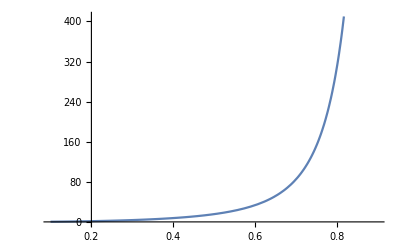

```mathematica
Plot[1/(2π)NIntegrate[Pd [β,t0,θ,φ]Sin[φ],{t0,0,2π},{θ,0,2π},{φ,0,π}],{β,0.1,0.9}]
```

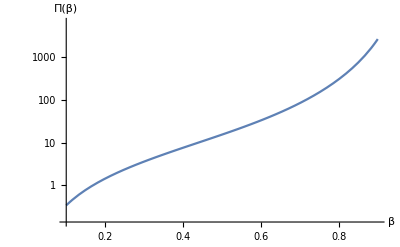

```mathematica
LogPlot[1/(2π)NIntegrate[Pd [β,t0,θ,φ]Sin[φ],{t0,0,2π},{θ,0,2π},{φ,0,π}],{β,0.1,0.9},AxesLabel->{"β","Π(β)"}]
```

for the case where there wasn’t any electric charge we had:

```mathematica
force=ω-> T/(γ^2 m β);
```

```mathematica
Simplify[ReplaceAll[ReplaceAll[ReplaceAll[PP,force],{T-> 1/(2π α),β->1}],{q1-> 1/(√137),α-> 0.9 GeV^-2}]]
```

(8.90592×10^43 GeV^4)/(m^2 γ^4)

```mathematica
τ[δE_,m_,β_]:=Block[{δt,γ=1/(√(1-β^2))},
δt=δt/.Solve[(8.905923343638973*^43 GeV^4)/(m^2 γ^4)==δE/δt,δt][[1]]/.{ MeV-> 10^6 eV,GeV-> 10^9 eV}/.eV-> (6.58 10^-16 s)^-1;
δt]
SetAttributes[τ,Listable];
Γ[δE_,m_,β_]:=Block[{δt,γ=1/(√(1-β^2))},
δt=δt/.Solve[(8.905923343638973*^43 GeV^4)/(m^2 γ^4)==δE/δt,δt][[1]]/.{GeV-> 10^3 MeV};
δt^-1]
SetAttributes[Γ,Listable];
```

```mathematica
Γ[100 MeV,100MeV,0.9999999999999999]
```

4.39096×10^18 MeV

```mathematica
100((α T^2)/(m^2 γ^4 β^2))/(Γ M)/.α-> 1/137/.T-> 0.17 GeV^2/.γ-> 1/(√(1-β^2))/.m-> 1000 MeV/.GeV-> 10^3 MeV/.β->0.7/.Γ->28 MeV/.M-> 2000 MeV
```

0.199956

```mathematica
24 137
```

3288

```mathematica
24.181558090932867 MeV/(930 MeV)
```

0.0260017

```mathematica
24.181558090932867 MeV/(135 MeV)
```

0.179123

```mathematica
1/(28.6 MeV)/.MeV->10^3 eV/.eV-> 1/6.58 10^16 s^-1
```

2.3007×10^-20 s

```mathematica
100/(γ^4 β^2)/.γ-> 1/(√(1-β^2))/.β->0.7
```

53.0816

### Alternative calculation based on the equations of motion

```mathematica
(q1 q2 β1^2 ω^2 (-2 Δθ Cos[Δθ]-2 (-1+Δθ^2) Sin[Δθ]+β1^2 (-2 Δθ+Sin[2 Δθ])))/(√(1-β1^2) (Δθ+β1^2 Sin[Δθ])^3)/.{β1->β,ω-> T/(γ^2 m β),Δθ->β}/.T-> 1/(2π α)/.α-> 0.9 10^-6 MeV^-2/.γ-> 1/(√(1-β^2))/.q1-> 1/(√137)/.q2-> 1/(√137)/.m-> mq MeV/.β-> 0.7
```

-(4.89424×10^7 MeV^2)/mq^2

```mathematica
Solve[%==-δE/δt,δt][[1,1]]/.δE-> 30 MeV/. MeV-> 10^6 eV/. eV-> (6.58 10^-16 s)^-1/.mq->100
```

δt→4.03331×10^-24 s

```mathematica
(4.8942414710^7 MeV^2)/(mq^2 200MeV)/.mq-> 100
```

0.0336332 MeV

```mathematica
F1//MatrixForm
```

(0 | -(q2 ω^3 (l1 (2+l2^2 ω^2) Cos[t ω]+l2 ((2-2 Δθ^2+l1^2 ω^2) Cos[Δθ-t ω]+l1 l2 ω^2 Cos[2 Δθ-t ω]+l1^2 ω^2 Cos[Δθ+t ω]-2 l1 l2 Δθ ω^2 Sin[t ω]+2 Δθ Sin[Δθ-t ω])))/(2 (Δθ+l1 l2 ω^2 Sin[Δθ])^3) | -(q2 ω^3 (2 l1 l2^2 Δθ ω^2 Cos[t ω]+2 l2 Δθ Cos[Δθ-t ω]+2 l1 Sin[t ω]+l1 l2^2 ω^2 Sin[t ω]-2 l2 Sin[Δθ-t ω]+2 l2 Δθ^2 Sin[Δθ-t ω]-l1^2 l2 ω^2 Sin[Δθ-t ω]-l1 l2^2 ω^2 Sin[2 Δθ-t ω]+l1^2 l2 ω^2 Sin[Δθ+t ω]))/(2 (Δθ+l1 l2 ω^2 Sin[Δθ])^3) | 0
(q2 ω^3 (l1 (2+l2^2 ω^2) Cos[t ω]+l2 ((2-2 Δθ^2+l1^2 ω^2) Cos[Δθ-t ω]+l1 l2 ω^2 Cos[2 Δθ-t ω]+l1^2 ω^2 Cos[Δθ+t ω]-2 l1 l2 Δθ ω^2 Sin[t ω]+2 Δθ Sin[Δθ-t ω])))/(2 (Δθ+l1 l2 ω^2 Sin[Δθ])^3) | 0 | -(l2 q2 ω^4 (l2+l1^2 l2 ω^2+l1 (1+l2^2 ω^2) Cos[Δθ]+l1 Δθ Sin[Δθ]))/((Δθ+l1 l2 ω^2 Sin[Δθ])^3) | 0
(q2 ω^3 (2 l1 l2^2 Δθ ω^2 Cos[t ω]+2 l2 Δθ Cos[Δθ-t ω]+2 l1 Sin[t ω]+l1 l2^2 ω^2 Sin[t ω]-2 l2 Sin[Δθ-t ω]+2 l2 Δθ^2 Sin[Δθ-t ω]-l1^2 l2 ω^2 Sin[Δθ-t ω]-l1 l2^2 ω^2 Sin[2 Δθ-t ω]+l1^2 l2 ω^2 Sin[Δθ+t ω]))/(2 (Δθ+l1 l2 ω^2 Sin[Δθ])^3) | (l2 q2 ω^4 (l2+l1^2 l2 ω^2+l1 (1+l2^2 ω^2) Cos[Δθ]+l1 Δθ Sin[Δθ]))/((Δθ+l1 l2 ω^2 Sin[Δθ])^3) | 0 | 0
0 | 0 | 0 | 0)

## Calculation based on spontaneous emmision (golden rule)

```mathematica
Γ[ΔE_,β_,m_]:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[(4 ΔE^3 l^2)/(3 137),l->β/ω], ω->1/(2π α m β γ^2) ],{α-> 0.9 GeV^-2,γ-> 1/(√(1-β^2))}],GeV-> 10^3 MeV];
SetAttributes[Γ,Listable];
τ[ΔE_,β_,m_]:=1/Γ[ΔE,β,m]/.MeV-> 10^6 eV/.eV-> (6.58 10^-16 s)^-1
SetAttributes[τ,Listable];
```

```mathematica
Γ[{20 MeV,30 MeV,200MeV,500 MeV,600 MeV},0.7,{100 MeV,100 MeV,100 MeV,100MeV,100MeV}]
```

{0.0000229829 MeV,0.0000775673 MeV,0.0229829 MeV,0.359108 MeV,0.620538 MeV}

```mathematica
τ[{20 MeV,30 MeV,200MeV,500 MeV,600 MeV},0.7,{100 MeV,100 MeV,100 MeV,100MeV,100MeV}]
```

{2.863×10^-17 s,8.48296×10^-18 s,2.863×10^-20 s,1.83232×10^-21 s,1.06037×10^-21 s}

```mathematica
(2/3(α^7 m^5 γ^4 β^4)/T^2 )/.α-> 1/137/.T-> 0.17 GeV^2/.γ-> 1/(√(1-β^2))/.m-> 1500 MeV/.GeV-> 10^3 MeV/.β->0.99
```

4.69092×10^-7 MeV